# PROJEKTNA NALOGA - Mathematica

Klavdija Koren, Fakulteta za matematiko in fiziko

## Izpitna pola 1 - MATEMATIKA, 8. junij 2019

https://www.ric.si/mma/M191-401-1-1/2019100912543968/

## 5. NALOGA

### Na sliki sta narisani premica p in krožnica k. Premica p poteka skozi točki A in B, premer krožnice k je daljica AB.

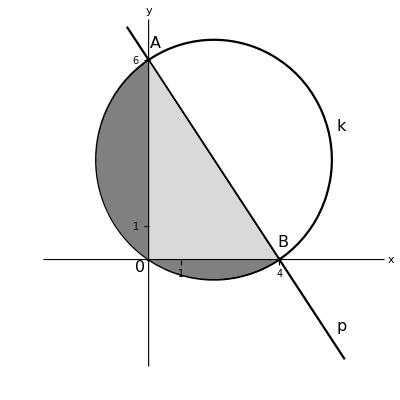

```mathematica
pts = NSolve[(x-2)^2 + (y-3)^2 ==  13 && y== ((-3)/2)x + 6 , {x,y}];
pts1 = NSolve[(x-2)^2 + (y-3)^2 ==  13 && x == 0,{x,y}];
Show[ContourPlot[{(x-2)^2 + (y-3)^2 ==  13 , y == ((-3)/2)x + 6}, {x,-3, 7}, {y, -3, 7}, ContourStyle->Black,Axes->True,AxesStyle->Black,AxesLabel->Automatic,LabelStyle->Medium,Frame->False,Ticks->{{{-3,},{-2,},{-1,},{0,},{1,1},{2,},{3,},{4,4},{5,},{6,},{7,}},{{-3,},{-2,},{-1,},{0,},{1,1},{2,},{3,},{4,},{5,},{6,6},{7,}}},TicksStyle->16],Graphics[{Black, PointSize[Large], Point[{x, y}/.pts], Point[{x, y}/.pts1],Gray,Disk[{1.97,2.985},√12.75,{Pi-ArcTan[3/2],2Pi-ArcTan[3/2]}], LightGray,Triangle[{{0,0},{3.96,0},{0,5.96}}],Text[Style["A",Italic, FontSize->16,Black], {0.2, 6.5}], Text[Style["B",Italic, FontSize->16,Black], {4.1, 0.5}],
Text[Style["k", Italic, FontSize->16, Black], {5.9, 4}],
Text[Style["p",Italic, FontSize->16, Black], {5.9, -2}],
Text[Style["0", FontSize->16,Black], {-0.25, -0.25}]}]
]
```

#### 5.1. Zapišite enačbo premice p.

```mathematica
A = {0, 6}; B = {4, 0};
k = (B[[2]] - A[[2]])/(B[[1]] - A[[1]]);
n = A[[2]]- k *A[[1]];
StringForm["k = ``", k]
StringForm["n = ``", n]
StringForm["enačba premice: y = `` x + ``", k, n]
```

k = -3/2

n = 6

enačba premice: y = -3/2 x + 6

#### 5.2. Zapišite enačbo krožnice k.

```mathematica
X = 2; Y = 3;
r  =  √(X^2+ Y^2);
StringForm["r = ``", r]
StringForm["enačba krožnice: (x - ``)^2 + (y - ``)^2 = ``", X, Y, r^2]
```

r = √13

enačba krožnice: (x - 2)^2 + (y - 3)^2 = 13

#### 5.3. Izračunajte vsoto ploščin osenčenih odsekov na sliki. Nalogo rešite brez uporabe računala.

```mathematica
a = 4; b = 6; 
St = (a * b)/2;
Sk = π * r^2;
So = Sk/2- St;
StringForm["S_TRIKOTNIKA= ``", St]
StringForm["S_KROGA= ``", Sk]
StringForm["S_OSENČENEGA= ``", So]
```

S_TRIKOTNIKA= 12

S_KROGA= 13 π

S_OSENČENEGA= -12+(13 π)/2

## 6. NALOGA

### V trikotniku ABC stranica AB meri 6 cm. Kot α = ∢BAC meri 70° in kot γ = ∢ACB meri 30°. Izračunajte dolžino stranice AC in ploščino trikotnika ABC. Rezultat zaokrožite na dve decimalki.

```mathematica
AB = 6; α = 70; γ = 30;
β = 180 - α - γ;
αrad = (α * Pi)/180;
βrad = (β * Pi)/180;
γrad = (γ * Pi)/180;
Subscript[V, a] =N[AB * Sin[βrad]];
AC = Subscript[V, a]/Sin[γrad];
S = (AB * AC * Sin[αrad])/2;
StringForm["β = ``°", β]
StringForm["V_a = `` cm",NumberForm[Subscript[V, a],{10,2}]]
StringForm["AC = `` cm", NumberForm[AC,{10,2}]]
StringForm["S = `` cm^2",NumberForm[S,{10,2}]]
```

β = 80°

V_a = 5.91 cm

AC = 11.82 cm

S = 33.31 cm^2

### Animacija:

```mathematica
Animate[Graphics[{FaceForm[LightGray],EdgeForm[{Thick,Darker[Blue,.6]}],Polygon[{{0,0},{AB,0},{(AB*Sin[βrad]*Cos[αrad ])/Sin[γrad],(AB*Sin[βrad]*Sin[αrad ])/Sin[γrad]}}],Text[Style["A",FontSize->14,Darker[Blue,.6],Bold],{-0.5,-0.5}],
Text[Style["B",FontSize->14,Darker[Blue,.6],Bold],{AB+0.5,-0.5}],Text[Style["C",FontSize->14,Darker[Blue,.6],Bold],{(AB*Sin[βrad]*Cos[αrad ])/Sin[γrad],(AB*Sin[βrad]*Sin[αrad ])/Sin[γrad]+0.5}],Text[Style["70°",FontSize->14,Darker[Blue,.6]],{1.3,0.7}],Text[Style["30°",FontSize->14,Darker[Blue,.6]],{(AB*Sin[βrad]*Cos[αrad ])/Sin[γrad]-0.2,(AB*Sin[βrad]*Sin[αrad ])/Sin[γrad]-3.1}],Text[Style["80°",FontSize->14,Darker[Blue,.6]],{AB-1.1,0.7}],
Text[Style[NumberForm[AB,{10,1}]" cm",FontSize->14,Darker[Blue,.6]],{AB/2,-0.8}],Text[Style[NumberForm[(AB*Sin[βrad])/Sin[γrad],{10,1}]" cm",FontSize->14,Darker[Blue,.6]],{(AB*Sin[βrad]*Cos[αrad ])/(2*Sin[γrad])-2,(AB*Sin[βrad]*Sin[αrad ])/(2*Sin[γrad])}],Text[Style[NumberForm[(AB*Sin[αrad])/Sin[γrad],{10,1}]" cm",FontSize->14,Darker[Blue,.6]],{(AB*Sin[βrad]*Cos[αrad ])/(2*Sin[γrad])+AB/2+2,(AB*Sin[βrad]*Sin[αrad ])/(2*Sin[γrad])}],Text[Style[StringForm["S = `` cm^2",NumberForm[(AB^2*Sin[αrad]*Sin[βrad])/Sin[γrad],{10,1}]],FontSize->14,Darker[Blue,.6],Bold],{1,21}]},PlotRange->{{-3,13},{-2,23}}],{AB,5,10,0.001,Appearance->"Labeled"},AnimationRate->0.2]
```

```mathematica
c=6; a=8;
Solve[(a*Sin[γmax])/c==1,γmax]
Animate[Graphics[{FaceForm[LightGray],EdgeForm[{Thick,Darker[Blue,.6]}],Polygon[{{0,0},{c,0},{√(a^2+c^2-2*a*c*Cos[Pi-γrad-ArcSin[a/c Sin[γrad]]])*√(1-(a/c Sin[γrad])^2),√(a^2+c^2-2*a*c*Cos[Pi-γrad-ArcSin[a/c Sin[γrad]]])*a/c Sin[γrad]}}],Text[Style["A",FontSize->14,Darker[Blue,.6],Bold],{-0.5,-0.5}],Text[Style["B",FontSize->14,Darker[Blue,.6],Bold],{c+0.5,-0.5}],Text[Style["C",FontSize->14,Darker[Blue,.6],Bold],{√(a^2+c^2-2*a*c*Cos[Pi-γrad-ArcSin[a/c Sin[γrad]]])*√(1-(a/c Sin[γrad])^2),√(a^2+c^2-2*a*c*Cos[Pi-γrad-ArcSin[a/c Sin[γrad]]])*a/c Sin[γrad]+0.5}],Text[Style[NumberForm[ArcSin[a/c Sin[γrad]]*180/Pi,{10,1}]"°",FontSize->14,Darker[Blue,.6]],{1.5,0.5}],Text[Style[NumberForm[(γrad*180)/Pi,{10,1}]"°",FontSize->14,Darker[Blue,.6]],{0.85*√(a^2+c^2-2*a*c*Cos[Pi-γrad-ArcSin[a/c Sin[γrad]]])*√(1-(a/c Sin[γrad])^2),0.8*√(a^2+c^2-2*a*c*Cos[Pi-γrad-ArcSin[a/c Sin[γrad]]])*a/c Sin[γrad]}],Text[Style[NumberForm[(Pi-γrad-ArcSin[a/c Sin[γrad]])*180/Pi,{10,1}]"°",FontSize->14,Darker[Blue,.6]],{c-0.8,0.5}],Text[Style["6 cm",FontSize->14,Darker[Blue,.6]],{c/2,-0.5}],Text[Style["8 cm",FontSize->14,Darker[Blue,.6]],{c-Cos[Pi-γrad-ArcSin[a/c Sin[γrad]]]*a/2+1,√(a^2+c^2-2*a*c*Cos[Pi-γrad-ArcSin[a/c Sin[γrad]]])*a/(2*c)Sin[γrad]}],Text[Style[NumberForm[√(a^2+c^2-2*a*c*Cos[Pi-γrad-ArcSin[a/c Sin[γrad]]]),{10,1}]" cm",FontSize->14,Darker[Blue,.6]],{0.35*√(a^2+c^2-2*a*c*Cos[Pi-γrad-ArcSin[a/c Sin[γrad]]])*√(1-(a/c Sin[γrad])^2),√(a^2+c^2-2a*c*Cos[Pi-γrad-ArcSin[a/c Sin[γrad]]])*a/(2*c)Sin[γrad]}],Text[Style[StringForm["S = `` cm^2",NumberForm[(a*c*Sin[Pi-γrad-ArcSin[a/c Sin[γrad]]])/2,{10,1}]],FontSize->14,Darker[Blue,.6],Bold],{0,9}]},PlotRange->{{-2,15},{-2,10}},ImageSize->700],{γrad,(10 Pi)/180,(42.8 Pi)/180,0.001,Appearance->"Labeled"},DefaultDuration->15]
```

{{γmax→ConditionalExpression[π-ArcSin[3/4]+2 π C[1], C[1]∈ℤ]},{γmax→ConditionalExpression[ArcSin[3/4]+2 π C[1], C[1]∈ℤ]}}